This . nb contains the code used to generate Figure 1 in arXiv : 2511.16196

```mathematica
<<MaTeX`
```

```mathematica
Clear["Global`*"]
```

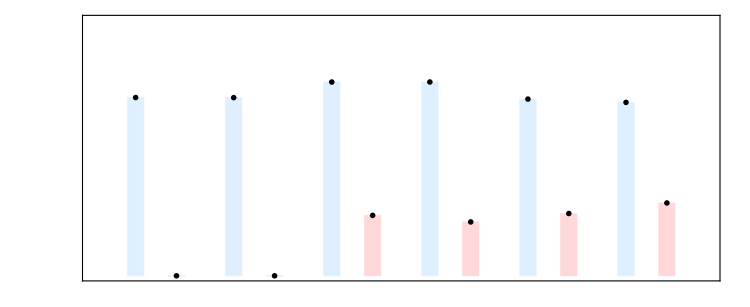

```mathematica
rawValues={{9761/(1500*28),0/(1500*24)},{9709/(1500*28),0/(1500*24)},{8708/(1500*13),29/(1500*12)},{8725/(1500*13),22/(1500*12)},{17616/(3000*27),68/(1500*26)},{15332/(3000*27),106/(1500*26)}};
customLabels={{MaTeX["\\frac{9761\\text{p}}{1500\\!\\cdot\\! 28\\text{ch}}",Magnification->1.34],
MaTeX["\\frac{0\\text{p}}{1500\\!\\cdot\\! 24\\text{ch}}",Magnification->1.34]},
{MaTeX["\\frac{9709\\text{p}}{1500\\!\\cdot\\! 28\\text{ch}}",Magnification->1.34],
MaTeX["\\frac{0\\text{p}}{1500\\!\\cdot\\! 24\\text{ch}}",Magnification->1.34]},
{MaTeX["\\frac{8708\\text{p}}{1500\\!\\cdot\\! 13\\text{ch}}",Magnification->1.34],
MaTeX["\\frac{29\\text{p}}{1500\\!\\cdot\\! 12\\text{ch}}",Magnification->1.34]},
{MaTeX["\\frac{8725\\text{p}}{1500\\!\\cdot\\! 13\\text{ch}}",Magnification->1.34],
MaTeX["\\frac{22\\text{p}}{1500\\!\\cdot\\! 12\\text{ch}}",Magnification->1.34]},
{MaTeX["\\frac{17616\\text{p}}{3000\\!\\cdot\\! 27\\text{ch}}",Magnification->1.34],
MaTeX["\\frac{68\\text{p}}{1500\\!\\cdot\\! 26\\text{ch}}",Magnification->1.34]},
{MaTeX["\\frac{15332\\text{p}}{3000\\!\\cdot\\! 27\\text{ch}}",Magnification->1.34],
MaTeX["\\frac{106\\text{p}}{1500\\!\\cdot\\!26\\text{ch}}",Magnification->1.34]}};


ticks=Table[{Subdivide[0.2+1.8,16.4,6][[i]],
Style[{MaTeX["\\tt{M1N1~M1I1}",Magnification->1.8],MaTeX["\\tt{M1N2~M1I2}",Magnification->1.8],
MaTeX["\\tt{M2N1~M2I1}",Magnification->1.8],MaTeX["\\tt{M2N2~M2I2}",Magnification->1.8],
MaTeX["\\tt{M3N1~M3I1}",Magnification->1.8],MaTeX["\\tt{M3N2~M3I2}",Magnification->1.8]}[[i]],16]},{i,1,6}];
plt=Show[BarChart[rawValues,ScalingFunctions->"Log10",ChartLabels->None,Ticks->{ticks,Automatic},(*ChartLegends->Placed[SwatchLegend[{MaTeX["\\text{NO}",Magnification->1.7],MaTeX["\\text{IO}",Magnification->1.7]},LegendLayout->"Row" ],{{0.04,0.98},{0,1}}],*)LabelingFunction->(Placed[Style[customLabels[[#2[[1]],#2[[2]]]],Bold,12,FontFamily->"Arial"],Above]&),ChartStyle->{LightBlue,LightRed},BarSpacing->{1.5,2.5},Frame->True,AspectRatio->0.41,GridLines->None,FrameTicksStyle->Directive[19,Black],PlotRange->{{0.5,15.5},{10^-3.9,6}},ImageSize->750,FrameStyle->Directive[Black,Thickness[0.0015]],FrameTicks->{{customYTicks,None},{ticks,None}}],FrameLabel->{{MaTeX["\\rm Scan~~ Efficiency~(p/ch)",Magnification->1.8],None},{None,None}}]
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"NI_compare.pdf"}],plt]
```

/Users/admin_phy/Desktop/GUT_Plot/Final/NI_compare_exp.pdf

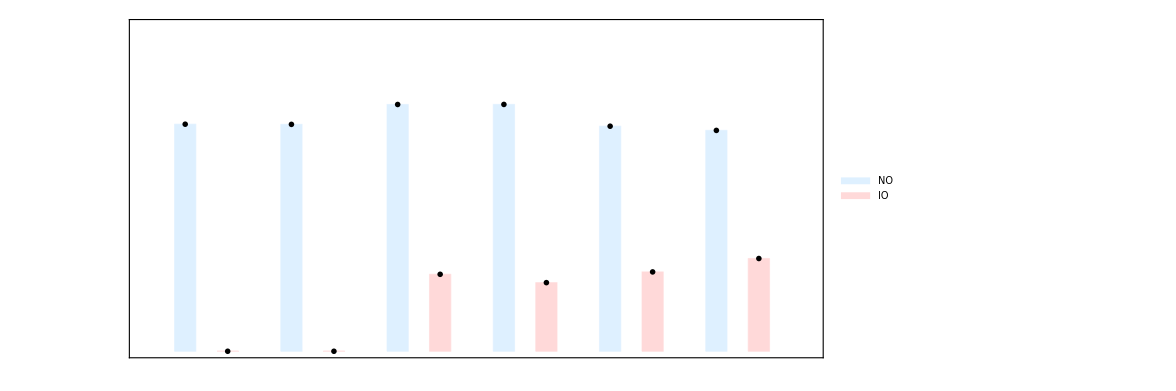

```mathematica
(*定义自定义纵坐标刻度*)customYTicks={{10^-3,MaTeX["10^{-3}",Magnification->1.8],{0.01,0},{}},{10^-2,MaTeX["10^{-2}",Magnification->1.8],{0.01,0},{}},{10^-1,MaTeX["10^{-1}",Magnification->1.8],{0.01,0},{}},{10^0,MaTeX["1",Magnification->1.8],{0.01,0},{}},(*修正处*){10^1,MaTeX["10^{1}",Magnification->1.8],{0.01,0},{}}};


customYTicks=Join[(*主刻度*){{10^-3,MaTeX["10^{-3}",Magnification->1.8],{0.01,0},{}},{10^-2,MaTeX["10^{-2}",Magnification->1.8],{0.01,0},{}},{10^-1,MaTeX["10^{-1}",Magnification->1.8],{0.01,0},{}},{10^0,MaTeX["1",Magnification->1.8],{0.01,0},{}},{10^1,MaTeX["10^{1}",Magnification->1.8],{0.01,0},{}}},(*小刻度：每个数量级内 2~9 倍*)Flatten[Table[{k*10^exp,"",{0.005,0},{}},{exp,{-4,-3,-2,-1,0}},{k,2,9}],1]];
plt=Show[BarChart[rawValues,ScalingFunctions->"Log10",ChartLabels->None,Ticks->{ticks,Automatic},(*可省略，因为 FrameTicks 已定义*)ChartLegends->Placed[SwatchLegend[{Style["NO",18],Style["IO",20]},LegendLayout->"Row"],{{0.04,0.93},{0,1}}],LabelingFunction->(Placed[Style[customLabels[[#2[[1]],#2[[2]]]],Bold,12,FontFamily->"Arial"],Above]&),ChartStyle->{LightBlue,LightRed},BarSpacing->{1,2},Frame->True,AspectRatio->0.45,GridLines->None,FrameTicksStyle->Directive[20,Black],PlotRange->{{0.5,16.2},{10^-3.9,6}},ImageSize->870,FrameStyle->Directive[Black,Thickness[0.0015]],FrameTicks->{{customYTicks,None},{ticks,None}}],FrameLabel->{{MaTeX["\\rm Scan~~ Efficiency~(p/ch)",Magnification->1.8],None},{None,None}}]
```